-Graphics-

```mathematica
(* Sets the working directory to the location of the notebook *)
SetOptions[$FrontEndSession,CellProlog:>Replace[Quiet[NotebookDirectory[]],{s_String?DirectoryQ:>SetDirectory[s],_:>$UserDocumentsDirectory}]]
```

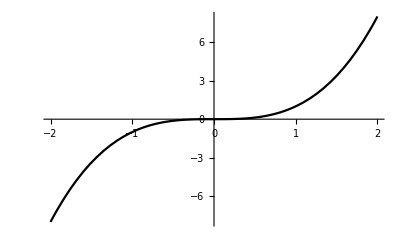

plots/ch2_xcubed.png

```mathematica
(* plot of f(x) = x^3 *)
ch2xcubed = Plot[x^3, {x, -2, 2}, PlotTheme ->"Monochrome"]
Export["plots/ch2_xcubed.png", ch2xcubed]
```

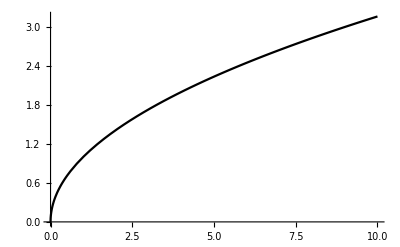

plots/ch2_concave.png

```mathematica
(* example of a concave function *)
ch2concave = Plot[Sqrt[x], {x, 0, 10}, PlotTheme -> "Monochrome"]
Export["plots/ch2_concave.png", ch2concave]
```

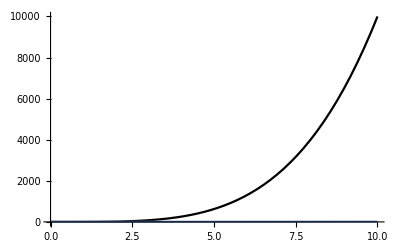

plots/ch2_convex.png

/Users/kevin/Documents/GitHub/ECON-1011A-Textbook

```mathematica
(* example of a convex function *)
ch2convex = Show[Plot[x^2, {x, 0, 10}, PlotTheme -> "Monochrome"], Plot[x, {x, 0, 10}]]
Export["plots/ch2_convex.png", ch2convex]
```